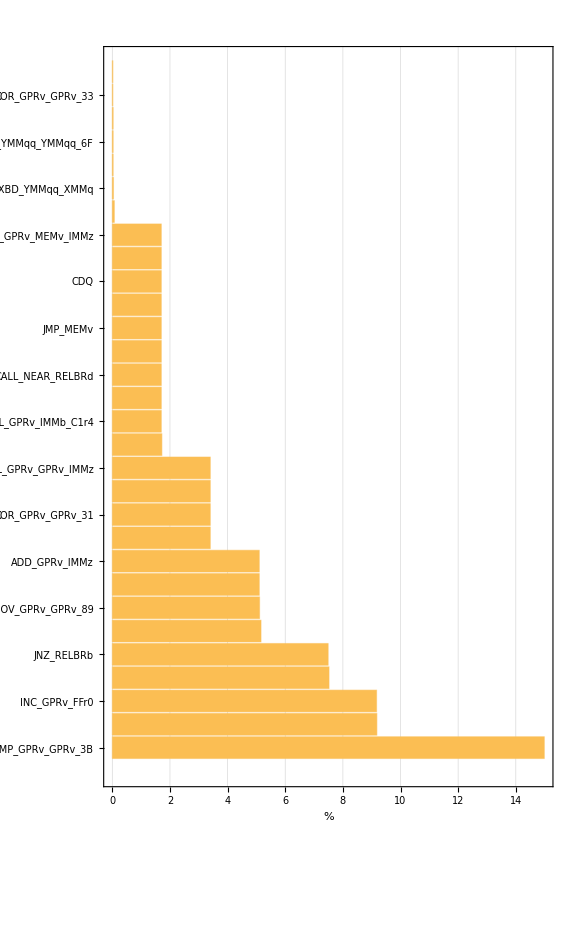
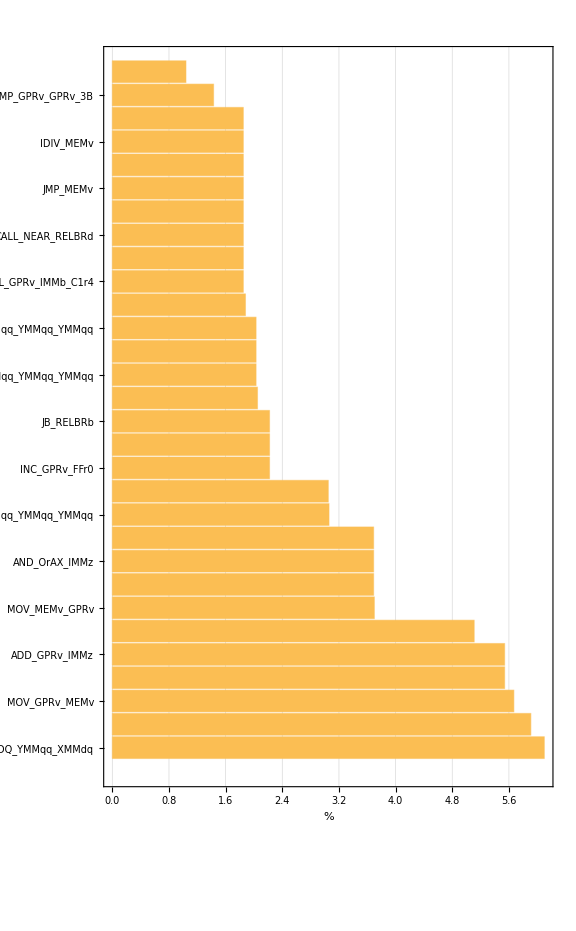
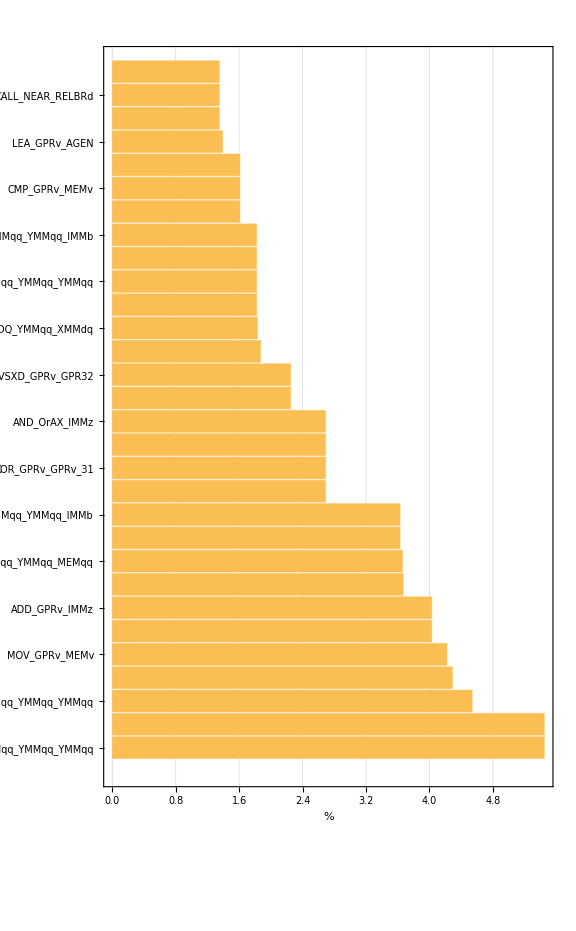

```mathematica
getChart[typelength_] := Module[{inp,top10,sum},inp = Import["!ssh arachnophobia cat /home/holger/Projects/compaction/sde-mix-out-"<>typelength<> ".txt | sed -n '/EMIT_GLOBAL_DYNAMIC_STATS/,$p' | egrep -v \"^#\" | egrep -v \"^\\*\" | grep -v total | sed -E \"s/ +/,/\"","CSV"]//Select[Length[#1]>1&]//SortBy[#1[[2]]&];
sum = inp//Map[#1[[2]]&]//Plus@@#1&;
inp//Map[#1[[1]]->#1[[2]]&]//Association//Select[#1>500&]//TakeLargest[30]//Map[Quantity[Round[#1*100/sum,.01],"%"]&]
]
{"16","32","64"}//Map[Function[bitwidth,(getChart[bitwidth]//BarChart[#1,PlotTheme->"Detailed",FrameLabel->{{"Instruction",None},{"%",bitwidth<> " Bit Integers"}},AspectRatio->GoldenRatio, ChartLabels->(#1//Keys),BarOrigin->Left, ImageSize->Large]&)]]
```